#### bin

```mathematica
AbsoluteTiming[
values=If[Head@Values[bin]===Association,First[Values[bin]],Values[bin]];
{ethV,exV,volV}=Transpose[{{#1,#2},{#1,#3},{#1,#5}}&@@@values];
{ethTS,exTS,volTS}=TimeSeries/@{ethV,exV,volV};
btcTS=ethTS/exTS;]
```

{18.9164,Null}

```mathematica
{firstTick,firstVal}=First@ethV
{lastTick,lastVal}=Last@ethV
```

{{2017,8,18,0,31,7.61},305.535}

{{2017,12,6,22,39,23.},436.996}

```mathematica
Now
DateDifference[Now,lastTick,"Minutes"]
```

Wed 6 Dec 2017 21:47:03GMT-6.

52.3203 min

DataDrop ticker is on -5 GMT. This was masked by Daylight Savings.

#### Forecast exchange rates

data = TemporalData[FinancialData["EUR/USD", {{2012, 5, 1}, {2012, 9, 30}}]]["Part", All, {{2012, 5, 1}, {2012, 9, 30}}];

```mathematica
{firstTick,lastTick}
```

{{2017,8,18,0,31,7.61},{2017,12,6,14,24,15.}}

```mathematica
windowHours
```

4

```mathematica
DatePlus[lastTick,-Quantity[4*windowHours,"Hours"]]
```

{2017,12,5,22,24,15}

```mathematica
With[{
start=DatePlus[lastTick,-Quantity[10*windowHours,"Hours"]],
end=DatePlus[lastTick,-Quantity[2*windowHours,"Hours"]]},
data = TemporalData[exV]["Part", All, {start, end}];
]
```

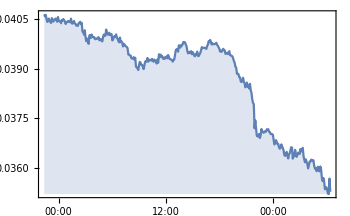

```mathematica
DateListPlot[data["Path"],Joined->True,Filling->Bottom,ImageSize->350]
```

ARIMAProcess[p,d,q] represents an ARIMA process with autoregressive and moving average orders p and q and integration order d
ARIMAProcess[40, 2, 0]

Simulate an ARIMA process with a linear trend:
ARIMAProcess[{-.1},1,{.2},.1]

Simulate an ARIMA process with a quadratic trend:
ARIMAProcess[.2,{-.6},2,{.8},.1]

ARIMAProcess[1,{.5},1,{.7},1]

Simulate with given precision:
ARIMAProcess[1/4,{2/10,1/10},2,{2/7},1/10]

Simulate a process with given initial values:
sproc[x_] := ARIMAProcess[0,{.6},1,{.3},1,{x}]

In the presence of a nonzero constant:
tproc[x_] :=  ARIMAProcess[0.2,{1.1},1,{.3},1,{x}]

Simulate a two-dimensional process:
ARIMAProcess[{α},{1,1},{β},Σ] 

Estimate process parameters:
sample = ARIMAProcess[.3, {.2}, 1, {.3}, .1]
eproc=EstimatedProcess[sample,ARIMAProcess[1,1]]
ARIMAProcess[0.283442,{0.241103},1,{0.292294},0.103912]

Use TimeSeriesModel to automatically find orders:
tsm = TimeSeriesModelFit[sample]
tsm[“Process”]
ARIMAProcess[0.26988,{0.277415},1,{0.257647},0.104042]

Forecast future values: (used by Finance Platform demo video)
ARIMAProcess[.4,{.3},2,{-.5},1]

The available methods for estimating an ARIMAProcess:
ARIMAProcess[.3,{.4},1,{.3},1]
methods = {Automatic,”MethodOfMoments”,”MaximumConditionalLikelihood”,
”MaximumLikelihood”,”SpectralEstimator”};

Method of moments admits the following solvers:
ARIMAProcess[{.4},1,{.3},1]
solvers = {Automatic,”FindRoot”,”NSolve”};

Maximum conditional likelihood method allows the following solvers:
ARIMAProcess[2,{.4},1,{.3},1]
solvers = {Automatic,”FindMaximum”,”NMaximize”};

Maximum likelihood method allows the following solvers:
ARIMAProcess[2,{.4,.2},1,{.3},1]
solvers = {Automatic,”FindMaximum”,”NMaximize”};

Spectral estimator allows to specify windows used for PowerSpectralDensity calculation:
ARIMAProcess[2,{.4,.2},1,{.3},1]
Spectral estimator allows following solvers:
ARIMAProcess[2,1]
solvers={Automatic,”FindMinimum”,”NMinimize”};

Multiple time slice distributions:
ARIMAProcess[1.2, {.2}, 1, {.3}, 1, { }]
ARIMAProcess[1, {.2}, 1, {.3}, 1]

First-order probability density function:
ARIMAProcess[1,{1/4},1,{1/3},1,{}]

Approximate with an MA process:
ARIMAProcess[.4,{.2,.3},4,{.1},1,{}]

Approximate with an AR process:
proc=ARIMAProcess[{.2,.3},1,{.5},1,{}];
aproc=ARProcess[proc,5]

Fit an ARIMA model to the time series:
ARIMAProcess[2, 1, 2]

Estimate an ARIMA with integration order equal to 1:
ARIMAProcess[1,1,1]

Forecast stock prices:
ARIMAProcess[3,1,0]

Simulate paths from an ARIMA process:
ARIMAProcess[.4,{.3},1,{.6},1]

There are zeros of the TransferFunctionModel on the unit circle:
ARIMAProcess[{.2},1,{.3,1},.2]

Or use exact values of parameters:
ARIMAProcess[{4/10},10,{-1/2},1,{}]

```mathematica
eproc=EstimatedProcess[data,ARIMAProcess[40,2,0]]
```

```mathematica
eproc=EstimatedProcess[data,ARIMAProcess[20,2,0]]
```

ARIMAProcess[-5.09841×10^-6,{-0.974474,-0.798523,-0.577625,-0.399166,-0.2931,-0.3233,-0.229721,-0.177058,-0.188844,-0.187062,-0.144078,-0.0457857,-0.0322499,0.047985,0.0390614,-0.0384977,-0.110884,-0.0574075,-0.0613949,-0.00517717},2,{},1.11112×10^-8]

```mathematica
eproc=EstimatedProcess[data,ARIMAProcess[10,2,0]]
```

ARIMAProcess[-4.32719×10^-6,{-0.967908,-0.785871,-0.566968,-0.384702,-0.274963,-0.294909,-0.178083,-0.105119,-0.0950925,-0.0630454},2,{},1.14284×10^-8]

```mathematica
eproc=EstimatedProcess[data,ARIMAProcess[.4,{.3},2,{-.5},1]]
```

```mathematica
eproc=EstimatedProcess[data,ARIMAProcess[1,1],
ProcessEstimator->"SpectralEstimator"]
```

ARIMAProcess[0.016678,{0.570075},0,{0.268258},3.26411×10^-7]

```mathematica
eproc=EstimatedProcess[data,ARIMAProcess[2,1,2]]
```

ARIMAProcess[-5.47862×10^-6,{0.921652,-0.302091},1,{-1.1428,0.539191},9.07747×10^-9]

```mathematica
eproc=EstimatedProcess[data,ARIMAProcess[3,1,0]]
```

ARIMAProcess[-0.0000162376,{-0.202213,-0.00559062,0.0802536},1,{},9.24526×10^-9]

```mathematica
2*windowHours*60/5
```

96

```mathematica
forecast=TimeSeriesForecast[eproc,data,{96}]
```

TemporalData[…]

```mathematica
With[{
start=DatePlus[lastTick,-Quantity[2*windowHours,"Hours"]],
end=lastTick},
update = TemporalData[exV]["Part", All, {start, end}];
]
```

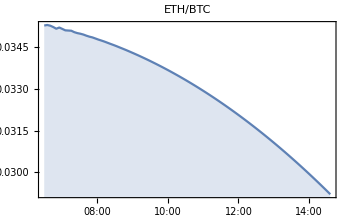

```mathematica
DateListPlot[forecast["Path"],
Joined->True,Filling->Axis,PlotLabel->"ETH/BTC",ImageSize->350]
```

```mathematica
DateListPlot[{
data["Path"],
forecast["Path"],
update["Path"]},
Joined->True,Filling->Axis,PlotLabel->"ETH/BTC",ImageSize->350]
```

ARIMAProcess[2,1,2] was

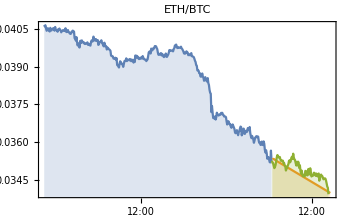

ARIMAProcess[3,1,0] was

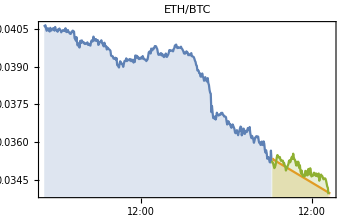

ARIMAProcess[1,1] was

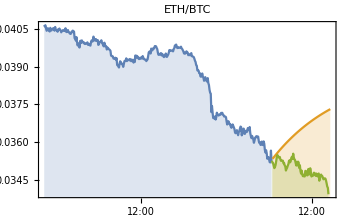

ARIMAProcess[40,2,0] was

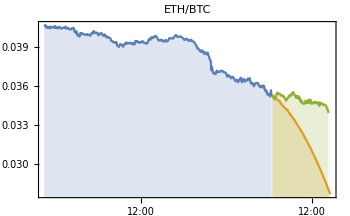

ARIMAProcess[20,2,0] was

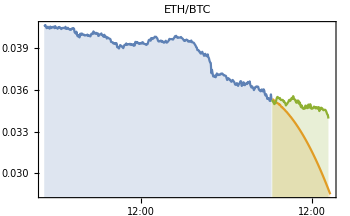

ARIMAProcess[10,2,0] was

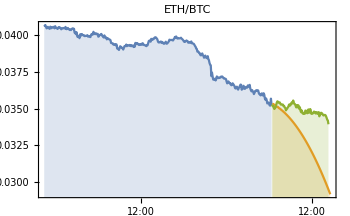

#### code

```mathematica
bin=Databin["nZWjPQuw"]
```

Databin[…]